```mathematica
fileName ="laser";
data = Import["C:\\p\\ann\\ex5\\"<>fileName<>".txt","CSV"];
dataT = Transpose[data];
 means=Mean/@ dataT
sdevs = StandardDeviation/@dataT

changeElem[x_, index_] := ((x-means[[index]])/sdevs[[index]]);
 changeRow[x_]:=(MapIndexed[changeElem,  x]); 
data = changeRow/@ data;
dataDone = N[data[[All, 1;;]]];

Export[fileName<>".csv",dataDone]
```

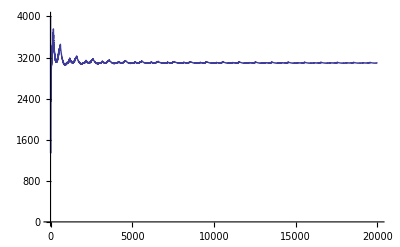

```mathematica
energy = ReadList["C:\\pg\\ffr135-ex5\energy.txt", {Number, Number}];ListLinePlot[energy[[1;;20000]], AxesOrigin->{0,0}, PlotRange->{0,4000}]
```